## Лабораторная работа №7 Крощук Виктор, ПО-5

## Задание 1: Элементарная описательная статистика

```mathematica
data=RandomReal[{10,50},10]
```

{32.676,20.3558,27.0094,19.9339,31.0192,33.757,41.095,39.1918,36.6712,11.5611}

```mathematica
Mean[data] (*Находит среднее значение*)
```

29.327

```mathematica
Median[data](*Находит значение медианты*)
```

31.8476

```mathematica
Max[data](*Находит максимальное значение*)
```

41.095

```mathematica
Variance[data](*Находит дисперсию*)
```

90.3503

```mathematica
StandardDeviation[data](*Находит среднеквадратичное отклонение*)
```

9.50528

```mathematica
Quantile[data,1](*Находит квантитиль. Её первым аргументом является набор данных;вторым аргументом является числоqв диапазоне от 0 до 1*)
```

31.0192

```mathematica
Quartiles[data](*Находит квантитили для списка*)
```

{20.3558,31.8476,36.6712}

## Задание 2: Работа со статистическими распределениями

```mathematica
PDF[NormalDistribution[μ,σ],x] (*дает функцию плотности вероятности для распределения, оцененного в точке x.*)
PDF[NormalDistribution[1,3],3]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

1/(3 ⅇ^(2/9) √(2 π))

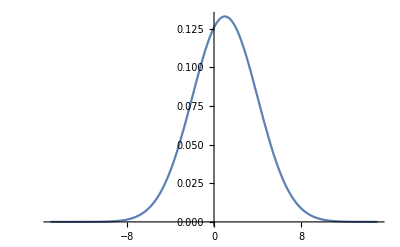

```mathematica
Plot[PDF[NormalDistribution[1,3],x],{x,-15,15}]
```

```mathematica
Mean[BinomialDistribution[1000,.1]]
```

100.

```mathematica
CharacteristicFunction[NormalDistribution[μ,σ],t] (*дает характеристическую функцию для распределения в зависимости от переменной t.*)
CharacteristicFunction[CauchyDistribution[μ,σ],t]  (*распределени коши*)
```

ⅇ^(ⅈ t μ-(t^2 σ^2)/2)

ⅇ^(ⅈ t μ-t σ Sign[t])

```mathematica
Moment[PoissonDistribution[μ],n](*дает n-й момент выборки элементов в списке.*)
Moment[CauchyDistribution[μ,σ],n]
```

Piecewise[{{BellB[n,μ], n≥0}, {0, True}}]

Piecewise[{{1, n==0}, {Indeterminate, True}}]

```mathematica
RandomVariate[ChiSquareDistribution[15],10] (*дает псевдослучайную переменную из символического распределения dist.*)
RandomVariate[PoissonDistribution[15],10]
RandomVariate[GeometricDistribution[1/3],20]
```

{13.413,11.0867,25.457,5.35215,6.43715,16.7204,14.7585,16.2784,13.0512,16.8648}

{17,10,16,16,18,17,20,9,7,17}

{1,3,5,0,0,4,2,0,1,0,6,1,1,0,0,1,10,4,1,1}

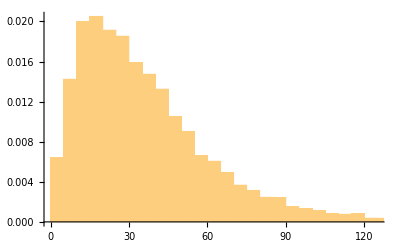

```mathematica
data=RandomVariate[GammaDistribution[2,18],10000];hist=Histogram[data,Automatic,"ProbabilityDensity"]
```

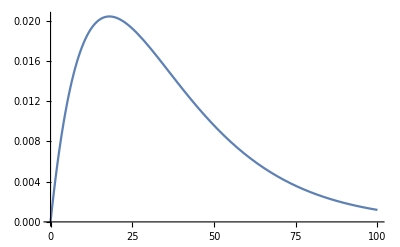

```mathematica
pl=Plot[PDF[GammaDistribution[2,18],x],{x,0,100}]
```

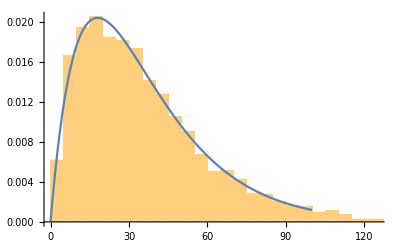

```mathematica
Show[hist,pl]
```

```mathematica
alphabeta=FindDistributionParameters[data,GammaDistribution[α,β]] (*находит оценки параметров для распределения dist по данным.*)
```

{α→1.98854,β→17.8676}

```mathematica
gdist=EstimatedDistribution[data,GammaDistribution[α,β]]
```

GammaDistribution[1.99514,18.1619]

```mathematica
LogLikelihood[gdist,gdata] (*gives the log-likelihood function for observations x1, x2, … from the distribution dist.*)
```

LogLikelihood[GammaDistribution[1.99514,18.1619],gdata]

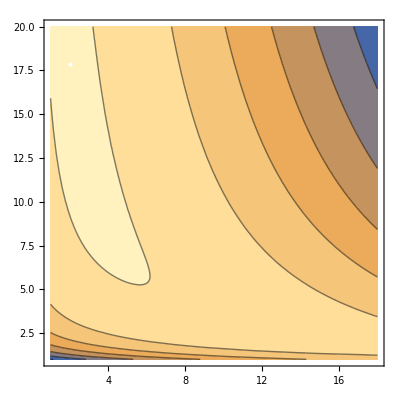

```mathematica
ContourPlot[LogLikelihood[GammaDistribution[α,β],data],{α,1,18},{β,1,20},Epilog->{White,Point[{α,β}/.alphabeta]}]
```

## Задание 3: Проверка гипотез о математическом ожидании

```mathematica
data = RandomVariate[NormalDistribution[17,4], 10]
```

{17.9774,13.5327,18.163,7.32535,8.87849,13.7861,15.3878,9.16073,23.7602,15.1487}

```mathematica
TTest[data, 17] (*проверяет, равно ли среднее значение данных нулю.*)
```

0.123452

```mathematica
TTest[data, 17, AlternativeHypothesis->"Less"]
```

0.287172

```mathematica
data2 = RandomVariate[NormalDistribution[9,1],10];
TTest[{data,data2}]
```

0.00832271

```mathematica
TTest[{data, data2},4,AlternativeHypothesis->"Less"]
```

0.785065

```mathematica
PairedTTest[{data,data2}] (*проверяет, равно ли среднее значение данных1- данных2 нулю.*)
```

0.0105102

```mathematica
Задание 4:Замена или удаление недостающих или недействительных данных
gdps=Map[CountryData[#,"GDP"]&,CountryData[All]];
(*Следующий код выдает валовой внутренний продукт (ВВП) для каждой страны, внесенной в перечень функции CountryData.*)
Take[gdps,10] (*Так выводятся значения gdps для первых 10 стран в алфавитном порядке:*)
{Quantity[1.91013538327371*^10, US dollars per year],Missing["NotAvailable"],Quantity[1.52780774468643*^10, US dollars per year],Quantity[1.69988236398126*^11, US dollars per year],Quantity[6.36*^8, US dollars per year],Quantity[3.15405798723833*^9, US dollars per year],Quantity[9.46354158699851*^10, US dollars per year],Quantity[2.111741492592593*^8, US dollars per year],Quantity[1.72775925925926*^9, US dollars per year],Quantity[4.49663446954073*^11, US dollars per year]}
Max[gdps] (*Максимум не может быть абсолютно точно определен по исходным данным:*)
Max::nord2: "Comparison of \!\(\*TagBox[TemplateBox[{\"2.14277`*^13\", RowBox[{FormBox[\"\\\"$\\\"\", TraditionalForm], \"\"}], RowBox[{\"\\\"per \\\"\", \"\", \"\\\"year\\\"\"}], \"US dollars per year\", FractionBox[\"\\\"USDollars\\\"\", \"\\\"Years\\\"\"]}, \"QuantityPrefixUnit\", SyntaxForm -> Mod], Short[#1, 5] & ]\) and \!\(\*TagBox[RowBox[{\"-\", \"∞\"}], Short[#1, 5] & ]\) is invalid."
Max[Missing["NotAvailable"],Quantity[2.14277*^13, US dollars per year]]
Count[gdps,_Missing] (*Количество отсутствующих значений в наборе данных может быть определено путем подсчета выражений с заголовком Missing.*)
16
Length[gdps] (*По сравнению с общим количеством данных в наборе (оно определено при помощи функции Length), количество отсутствующих значений относительно невелико*)
249
filteredgdps=DeleteCases[gdps,_Missing]; (*удаление всех элементов _Missing*)
{Length[filteredgdps],Max[filteredgdps]} (*длина оставшихся данных и максимальное значение*)
{0,filteredgdps}
data={{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{4,88.6,1.9},{1,62.3,1.8},{1,82.7,"NA"},{1,35.5,1.84}}; (* дан набор данных, где первый элемент представляет номер одной из двух групп, а два других элемента являются численными результатами измерений свойств отдельных объектов в этих группах*)
Grid[data,Dividers->All] (*Отображение данных в табличной форме облегчает задачу поиска "проблемных" данных:*)
{{1, 71.6, 0.41}, {2, 27.2, 4.96}, {2, 59.3, 0.18}, {1, 46., 2.72}, {2, 42.2, 1.06}, {1, 89.1, 3.75}, {4, 88.6, 1.9}, {1, 62.3, 1.8}, {1, 82.7, "NA"}, {1, 35.5, 1.84}}
baddata[entry_]:=Not[MatchQ[entry,{1|2,_?NumberQ,_?NumberQ}]] (*идентифицирует такие элементы данных, проверяя соответствие данных на входе заданному шаблону. Она возвращает значение True (Истина) если данные на входе не совпадают с шаблоном:*)
DeleteCases[data,_?baddata]
{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,35.5,1.84}}
badgroup[entry_]:=Not[MatchQ[entry[[1]],1|2]]
filtereddata=DeleteCases[data,_?badgroup] (*Для удаления недействительных данных, используем функцию DeleteCases с выражением _?baddata в качестве шаблона:*)
{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,"NA"},{1,35.5,1.84}}
group1=Select[filtereddata,#[[1]]===1&] (*Используем функцию Select для выборки элементов данных группы 1*)
{{1,71.6,0.41},{1,46.,2.72},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,"NA"},{1,35.5,1.84}}
group1mean=Mean[Select[group1[[All,-1]],NumberQ]] (*Используем функцию Select вновь, для выборки чисел из последнего элемента каждой записи (третьего столбца) списка данных group1, и рассчитаем их среднее значение:*)
2.104
filtereddata[[All,3]]=filtereddata[[All,3]]/."NA"->group1mean (*Теперь воспользуемся правилом подстановки для замены NA найденным средним значением*)
{0.41,4.96,0.18,2.72,1.06,3.75,1.8,2.104,1.84}
Grid[filtereddata,Dividers->All] (*Применим функцию Grid для отображения отфильтрованных данных*)
{{1, 71.6, 0.41}, {2, 27.2, 4.96}, {2, 59.3, 0.18}, {1, 46., 2.72}, {2, 42.2, 1.06}, {1, 89.1, 3.75}, {1, 62.3, 1.8}, {1, 82.7, "NA"}, {1, 35.5, 1.84}}
replaceByGroup[data_,col_,groupcol_,f_]:=Block[{columnvals,funvals,grouped,groups,rules},columnvals=data[[All,{groupcol,col}]];
If[VectorQ[columnvals[[All,2]],NumericQ],
columnvals[[All,2]],
grouped=GatherBy[columnvals,First];
groups=grouped[[All,1,1]];
funvals=Table[f[Select[grouped[[i]][[All,2]],NumericQ]],{i,Length[groups]}];
rules=Table[Rule[{groups[[i]],_?(Not[NumericQ[#]]&)},{groups[[i]],funvals[[i]]}],{i,Length[groups]}];
Replace[columnvals,rules,{1}][[All,2]]]]

newdata=DeleteCases[data,_?badgroup]

{{1,71.6,0.41},{2,27.2,4.96},{2,59.3,0.18},{1,46.,2.72},{2,42.2,1.06},{1,89.1,3.75},{1,62.3,1.8},{1,82.7,"NA"},{1,35.5,1.84}}
replaceByGroup[newdata,3,1,Mean]
{0.41,4.96,0.18,2.72,1.06,3.75,1.8,2.104,1.84}
replaceByGroup[newdata,3,1,Median]
{0.41,4.96,0.18,2.72,1.06,3.75,1.8,1.84,1.84}
Grid[Transpose[Table[If[j==1,newdata[[All,j]],replaceByGroup[newdata,j,1,Mean]],{j,Length[newdata[[1]]]}]]]
{{1, 71.6, 0.41}, {2, 27.2, 4.96}, {2, 59.3, 0.18}, {1, 46., 2.72}, {2, 42.2, 1.06}, {1, 89.1, 3.75}, {1, 62.3, 1.8}, {1, 82.7, 2.104}, {1, 35.5, 1.84}}
Grid[Transpose[{newdata[[All,1]],replaceByGroup[newdata,2,1,Mean],replaceByGroup[newdata,3,1,Median]}]]
{{1, 71.6, 0.41}, {2, 27.2, 4.96}, {2, 59.3, 0.18}, {1, 46., 2.72}, {2, 42.2, 1.06}, {1, 89.1, 3.75}, {1, 62.3, 1.8}, {1, 82.7, 1.84}, {1, 35.5, 1.84}}
```

## Задание 5: Работа со столбцами данных

```mathematica
data = BlockRandom[SeedRandom[8];RandomInteger[{8, 20},{5,5}]]
```

{{8,10,12,20,16},{11,14,8,15,10},{15,15,20,13,15},{12,17,13,16,20},{18,11,11,8,13}}

```mathematica
MatrixForm[data] (*печатает с элементами списка, расположенными в обыном регулярном массиве.*)
```

(8 | 10 | 12 | 20 | 16
11 | 14 | 8 | 15 | 10
15 | 15 | 20 | 13 | 15
12 | 17 | 13 | 16 | 20
18 | 11 | 11 | 8 | 13)

```mathematica
Grid[data]
```

8 | 10 | 12 | 20 | 16
11 | 14 | 8 | 15 | 10
15 | 15 | 20 | 13 | 15
12 | 17 | 13 | 16 | 20
18 | 11 | 11 | 8 | 13

```mathematica
Mean[data](*среднее арифметическое каждой колонки*)
StandardDeviation[data] (*дает выборочное стандартное отклонение элементов в списке.*)
Median[data]
```

{64/5,67/5,64/5,72/5,74/5}

{7 √(3/10),√(83/10),√(197/10),√(193/10),√(137/10)}

{12,14,12,15,15}

```mathematica
col =data[[All, 5]](*получаем колонку*)
Mean[col]
StandardDeviation[col]
```

{16,10,15,20,13}

74/5

√(137/10)

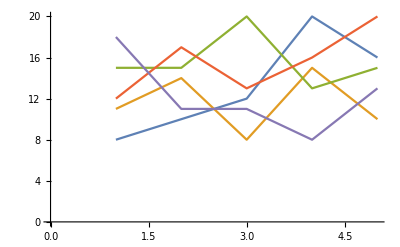

```mathematica
ListLinePlot[data]
```

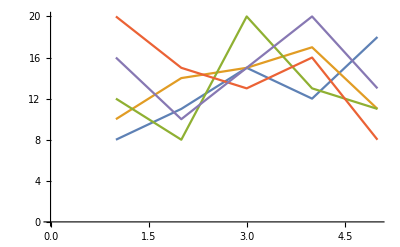

```mathematica
ListLinePlot[ Transpose[data]]
```

```mathematica
Map[Normalize,Transpose[data]] (*применяет f к каждому элементу первого уровня в expr. Для функций,работающих с векторами,применим функцию к транспонированным данным используя команду Map для вычислений на столбцах:*)
```

{{4 √(2/439),11/(√878),15/(√878),6 √(2/439),9 √(2/439)},{10/(7 √19),2/(√19),15/(7 √19),17/(7 √19),11/(7 √19)},{6 √(2/449),4 √(2/449),10 √(2/449),13/(√898),11/(√898)},{10 √(2/557),15/(√1114),13/(√1114),8 √(2/557),4 √(2/557)},{(8 √(2/23))/5,√(2/23),3/(√46),2 √(2/23),13/(5 √46)}}

```mathematica
Transpose[%]
```

{{4 √(2/439),10/(7 √19),6 √(2/449),10 √(2/557),(8 √(2/23))/5},{11/(√878),2/(√19),4 √(2/449),15/(√1114),√(2/23)},{15/(√878),15/(7 √19),10 √(2/449),13/(√1114),3/(√46)},{6 √(2/439),17/(7 √19),13/(√898),8 √(2/557),2 √(2/23)},{9 √(2/439),11/(7 √19),11/(√898),4 √(2/557),13/(5 √46)}}

```mathematica
Map[Max,Transpose[data]]
```

{18,17,20,20,20}

## Задание 6: Выполнение операций с подгруппами данных

```mathematica
(*Следующие данные представляют урожайность для трех типов грунта и двух сортов семян*)
```

```mathematica
agdata={{clay,seedB,175},{silty,seedB,180},{clay,seedB,165},{sandy,seedA,168},{clay,seedA,184},{sandy,seedB,171},{sandy,seedB,173},{sandy,seedA,189},{clay,seedA,186},{silty,seedB,174},{clay,seedA,192},{clay,seedA,184},{clay,seedA,179},{sandy,seedA,182},{sandy,seedB,177},{silty,seedA,180},{clay,seedB,175},{silty,seedB,181},{sandy,seedA,176},{silty,seedB,190}};
```

```mathematica
bySoilType=GatherBy[agdata,First] (*собирает в подсписки каждый набор элементов списка, который дает одинаковое значение при применении f. делают выборку в подсписки по первому элементу каждой точки данных*)
```

{{{clay,seedB,175},{clay,seedB,165},{clay,seedA,184},{clay,seedA,186},{clay,seedA,192},{clay,seedA,184},{clay,seedA,179},{clay,seedB,175}},{{silty,seedB,180},{silty,seedB,174},{silty,seedA,180},{silty,seedB,181},{silty,seedB,190}},{{sandy,seedA,168},{sandy,seedB,171},{sandy,seedB,173},{sandy,seedA,189},{sandy,seedA,182},{sandy,seedB,177},{sandy,seedA,176}}}

```mathematica
Table[{x[[1,1]],N[Mean[x[[All,-1]]]]},{x,bySoilType}]
(*Среднее число для каждого типа может быть вычислено путем извлечения каждого типа из каждого подсписка и вычисления среднего Mean значения последнего элемента в списке.  Для решения задачи можно воспользоваться функцией Table при трёх группах в качестве значения для итератора переменной x. (Средняя урожайность для каждого типа почвы.Применим функциюTableдля вывода типа грунта и средней урожайности для каждой группы)*)
```

{{clay,180.},{silty,181.},{sandy,176.571}}

```mathematica
(*Для получения информации об урожайности в зависимости от сорта семян,сгруппируем,для начала,данные по второму элементу каждой точки данных. Воспользуемся чистой функцией#[[2]]&вместе с GatherBy,для выборки данных по сорту семян:*)
bySeedType=GatherBy[agdata,#[[2]]&]
```

{{{clay,seedB,175},{silty,seedB,180},{clay,seedB,165},{sandy,seedB,171},{sandy,seedB,173},{silty,seedB,174},{sandy,seedB,177},{clay,seedB,175},{silty,seedB,181},{silty,seedB,190}},{{sandy,seedA,168},{clay,seedA,184},{sandy,seedA,189},{clay,seedA,186},{clay,seedA,192},{clay,seedA,184},{clay,seedA,179},{sandy,seedA,182},{silty,seedA,180},{sandy,seedA,176}}}

```mathematica
MatrixForm
```

```mathematica
(*{{{clay,seedB,175},
{silty,seedB,180},
{clay,seedB,165},
{sandy,seedB,171},
{sandy,seedB,173},
{silty,seedB,174},
{sandy,seedB,177},
{clay,seedB,175},
{silty,seedB,181},
{silty,seedB,190}}*)
```

```mathematica
(*Вычисление среднего в разрезе сортов семян очень похоже на процедуру,использованную для получения данных в разрезе типа почвы.Однако,при этом был использован только что сформированный набор данныхbySeedType.И,кроме того,был взят второй элемент для получения сорта семян. Воспользуемся функциейTableдля вычисления средней урожайности для каждого сорта семян:*)
Table[{x[[1,2]],N[Mean[x[[All,-1]]]]},{x,bySeedType}]
```

{{seedB,176.1},{seedA,182.}}

```mathematica
(*можно узнать диапазон урожайности и минимальную и максимальную урожайность в зависимости от сорта семян. Так вычисляется минимальная и максимальная урожайность для каждого сорта семян*)
Table[{x[[1,2]],{N[Min[x[[All,-1]]]],N[Max[x[[All,-1]]]]}},{x,bySeedType}]
```

{{seedB,{165.,190.}},{seedA,{168.,192.}}}

```mathematica
(*Проверка*)
```

```mathematica
Table[{y[[10,2]],{N[Min[y[[All, 3]]]],N[Max[y[[All,3]]]]}},{y,bySeedType}]
```

{{seedB,{165.,190.}},{seedA,{168.,192.}}}

## Задание 7: Выполнение линейной регрессии

```mathematica
(*Линейная модель предсказывает значение зависимой переменной от линейной комбинации предикторных (прогнозируемых) переменных или функций предикторных переменных.ВMathematica,функцияLinearModelFitвозвращает объект,содержащий данные подбора по точкам для модели линейной регрессии,и позволяет легко извлекать результаты и проводить диагностику.*)
```

```mathematica
(*Сформируем набор данных:*)
```

```mathematica
data = Table[{3 + i + RandomReal[{-3, 7}], i + RandomReal[{-2, 5}]}, {i, 1, 20}];
model=LinearModelFit[data,x,x]
(*Воспользуемся функцией LinearModelFit для создания линейной модели для заданного набора данных:*)
```

FittedModel[-1.03381+0.860882 x]

```mathematica
model["BestFit"] (*Извлечем функциональную форму модели:*)
```

-1.03381+0.860882 x

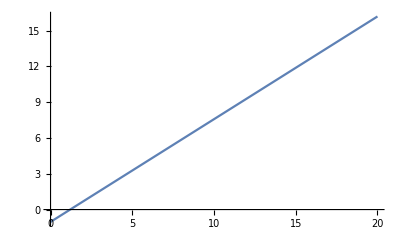

```mathematica
Plot[model["BestFit"], {x, 0, 20}] (*Построим график функциональной формы модели*)
```

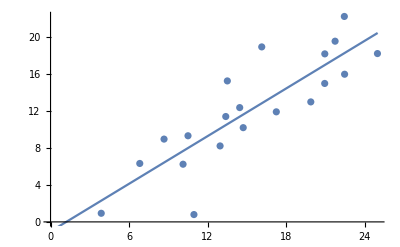

```mathematica
Show[ListPlot[data], Plot[model["BestFit"], {x, 0, 25}]] (*Отобразим данные и линию наилучшего соответствия:*)
```

```mathematica
model["ParameterTable"] (*Получим информацию по оценке параметров выполненной регрессии:*)
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.03381 | 2.06246 | -0.50125 | 0.62227
x | 0.860882 | 0.125924 | 6.8365 | 2.12826×10^-6

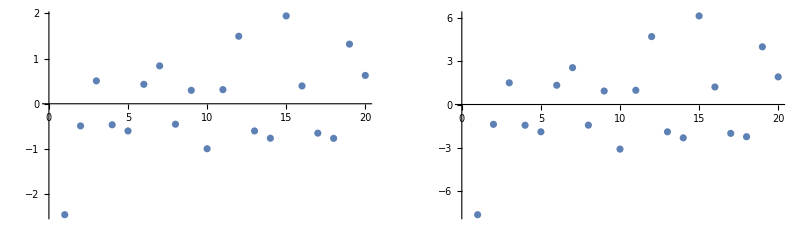

```mathematica
{sr,fr}=model[{"StandardizedResiduals", "FitResiduals"}]; (*Извлечем и отобразим на графике нормализованные и наблюдаемые невязки:*)
{{ListPlot[sr], ListPlot[fr]}}//GraphicsGrid
```

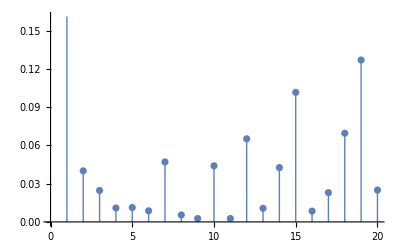

```mathematica
ListPlot[model["CookDistances"], Filling->Axis, FillingStyle->Thick, PlotStyle->Thick] (*Построим график расстояний Кука:*)
```

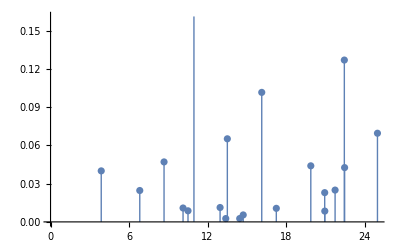

```mathematica
ListPlot[Transpose[{data[[All, 1]], model["CookDistances"]}], Filling->Axis, FillingStyle->Thick, PlotStyle->Thick] (*Как вариант, построим график расстояний Кука в зависимости от предикторного значения:*)
```